# Chirped Detuned Raman Transfer

## Gabriel Patenotte || September 2, 2021 || Ni Group

## Notebook setup

```mathematica
Remove["Global`*"](*Clears all variables*)
padding={{70, 10}, {50, 10}}; (*Extra space surrounding a plot. Needs to be defined, else plots of the same ImageSize won't line up.*)
size=500; (*Size used for the ImageSize parameter*)
SetOptions[Plot,BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,ImagePadding->padding,ImageSize->size]; (*Sets Plots to have a certain look*)
SetOptions[ListPlot,BaseStyle->{FontFamily->"Optima",FontSize->16},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,Joined->True,FrameTicks->{Automatic,Automatic},ImagePadding->padding,ImageSize->size]; (*Sets ListPlots to have a certain look*)
```

## Physics setup

```mathematica
μs=10^-6; (*Units*)
MHz=10^6; (*Units*)
GHz=10^9; (*Units*)
Γ=2π 100 MHz; (*Scattering from intermediate states*);
Δp=2π  21GHz; (*Detuning of the pump beam*)
range=20; (*Frequency range, in MHz, that the experiment can be chirped*);
ranget={0,40,.05};(*Range (in μs) and steps size (in μs) over which the ndsolve calculates the population in each state*)
H[t_,Ωs_,Ωp_,Δ0_,Δ1_]=({{0, 1/2 Ωp, 1/2 √12 Ωp, 0}, {1/2 Ωp, Δp-ⅈ Γ/2, 0, 1/2 Ωs}, {1/2 √12 Ωp, 0, Δp+2π 3.4 GHz-ⅈ Γ/2, 0}, {0, 1/2 Ωs, 0, Δ0+Δ1 t}}); (*Hamiltonian for a 4-level Λ system, with two excited intermediate states.*)
```

## Modules

```mathematica
findPops[Ωs0_,Ωp0_,Δ00_,Δ10_]:=Module[{Ωs=Ωs0,Ωp=Ωp0,Δ0=Δ00,Δ1=Δ10},
P[t_]={p1[t],p2[t],p3[t],p4[t]};
(*The population in each of the four bare basis state*)
init=P[0]=={1,0,0,0};(*The population initially resides in the initial state*) 
SE=ⅈ P'[t]==H[t,Ωs,Ωp,Δ0,Δ1].P[t];(*The Schrodinger equation*)
sols=NDSolveValue[{SE,init},{p1,p2,p3,p4},{t,0,50 μs},PrecisionGoal->7,Method->"ImplicitRungeKutta"];(*We solve the Schrodinger equation. The Method is chosen to significantly reduce the evaluation time.*)
pops=Abs[#[t μs]&/@sols]^2 (*The population in each state as a function of time. The use of # here gives each of the four outputs of sols an argument of t in μs.*);{lp1,lp2,lp3,lp4}=Table[Table[{t,pops⟦i⟧},Evaluate@Flatten[{t,ranget}]],{i,1,4}](*Data for a ListPlot of the four populations over time.*)]
```

```mathematica
findACShift[Ωs0_,Ωp0_]:=Module[{Ωs=Ωs0,Ωp=Ωp0},
P[t_]={p1[t],p2[t],p3[t],p4[t]};(*The population of the four states*)
init=P[0]=={1,0,0,0};(*The population is initially in the initial state*)
SE=ⅈ P'[t]==H[t,Ωs,Ωp,Δ0,0].P[t];(*The Schodinger equation*)
sols=ParametricNDSolveValue[{SE,init},{p1,p2,p3,p4},{t,0,50 μs},{Δ0},PrecisionGoal->7,Method->"ImplicitRungeKutta"];(*A parametric NDsolver, that gives a time-dependent solution as a function of Δ0*)
rangeΔ={-5,10,3}; (*The population in the initial state is checked over a range of Δ0s. This defines that range.*)
n=1;
While[n<11,
popΔ=Table[Abs[sols[Δ MHz]⟦1⟧[.1μs]]^2,Evaluate@Flatten[{Δ,rangeΔ}]](*A table of the population in the initial state at 0.1μs, depending on Δ0. We choose a time that is much less than a π pulse. The Δ0 that corresponds with the lowest initial population is the 2-photon AC stark shift.*);
Δs=Table[Δ,Evaluate@Flatten[{Δ,rangeΔ}]];
minLoc=Δs⟦Ordering[popΔ,1]⟦1⟧⟧;(*The Δ0 in the current range that corresponds with the greatest population transfer. The 2-photon resonance should be a step size away from this point.*)
rangeΔ={minLoc-rangeΔ⟦3⟧,minLoc+rangeΔ⟦3⟧,2rangeΔ⟦3⟧/6};(*We specify a new range that zooms in around the minLoc.*) n++];
minLoc//N(*The while loop narrows down on a more precise range of Δ0s, such that the final minLoc is the AC stark shift up to several significant figures.*)]
```

## Output

```mathematica
shift=findACShift[2π 222 MHz,2π 37 MHz](*The 2-photon resonance for these particular pump and stokes Rabi frequencies*)
```

2.6307

```mathematica
findACShift[1.04 2π 222 MHz,1.04 2π 37 MHz]-shift
```

0.206219

```mathematica
findACShift[0.96 2π 222 MHz,0.96 2π 37 MHz]-shift
```

-0.197988

```mathematica
bestParam[Δ00_,Δ10_]:=Module[{Δ0=Δ00,Δ1=Δ10},
allowedIndices=Abs[1+Round[range/Δ1 1/ranget⟦3⟧]]//Quiet;(*Experimentally, the extent that we change the 2-photon detuning with AOMs, the range, is constrained. The allowedIndices selects for pulses within the range.*)
allowedPop=findPops[2π 222 MHz,2π 37 MHz,Δ0 MHz,Δ1 MHz/μs]⟦4⟧⟦;;Min[allowedIndices,ranget⟦2⟧/ranget⟦3⟧]⟧;(*We restrict the population within allowed range. The Min is there in the case that the range is 0, which would make allowedIndices infinite.*)
pos=Ordering[allowedPop⟦All,2⟧,-1]⟦1⟧;(*Finds the position of the maximum population*) 
allowedPop⟦pos⟧ (*Outputs the time and population when the population is largest.*)]

bestΔ1[Δ00_]:=Module[{Δ0=Δ00},
rangeΔ1={2.5,6,2.5};(*For each Δ0, we want to find the optimal Δ1 that will lead to the most population transfer. This is the range of Δ1s that we consider.*)
n=1;
While[n<6,
popΔ1=Table[bestParam[Δ0,Δ1]⟦2⟧,Evaluate@Flatten[{Δ1,rangeΔ1}]];
Δ1s=Table[Δ1,Evaluate@Flatten[{Δ1,rangeΔ1}]];
maxLoc=Δ1s⟦Ordering[popΔ1,-1]⟦1⟧⟧;
rangeΔ1={maxLoc-rangeΔ1⟦3⟧,maxLoc+rangeΔ1⟦3⟧,rangeΔ1⟦3⟧/4};n++];(*The code here is the same as in findACShift*)

{bestParam[Δ0,maxLoc],N[maxLoc]}]
```

```mathematica
optimal=Table[{Δ0,bestΔ1[Δ0]},{Δ0,shift-10,shift,.1}]
```

{{-7.40625,{{10.7,0.937097},1.11328}},{-7.30625,{{10.75,0.937239},1.09375}},{-7.20625,{{10.85,0.937323},1.07422}},{-7.10625,{{10.8,0.937152},1.06445}},{-7.00625,{{10.9,0.937053},1.04492}},{-6.90625,{{10.95,0.936985},1.02539}},{-6.80625,{{9.9,0.939526},1.14258}},{-6.70625,{{9.95,0.939847},1.12305}},{-6.60625,{{10.15,0.940062},1.09375}},{-6.50625,{{10.1,0.940212},1.08398}},{-6.40625,{{8.9,0.939278},1.24023}},{-6.30625,{{9.,0.940422},1.21094}},{-6.20625,{{10.3,0.939908},1.02539}},{-6.10625,{{10.35,0.9399},1.00586}},{-6.00625,{{9.2,0.942962},1.14258}},{-5.90625,{{9.25,0.94331},1.12305}},{-5.80625,{{9.4,0.94339},1.09375}},{-5.70625,{{9.45,0.943299},1.07422}},{-5.60625,{{8.1,0.941791},1.26953}},{-5.50625,{{8.2,0.943349},1.24023}},{-5.40625,{{8.3,0.944521},1.21094}},{-5.30625,{{9.65,0.9428},0.996094}},{-5.20625,{{8.4,0.946318},1.16211}},{-5.10625,{{8.5,0.946753},1.13281}},{-5.00625,{{8.5,0.946995},1.11328}},{-4.90625,{{8.55,0.946948},1.09375}},{-4.80625,{{8.55,0.947058},1.07422}},{-4.70625,{{8.65,0.9468},1.04492}},{-4.60625,{{7.35,0.94608},1.26953}},{-4.50625,{{7.4,0.94787},1.24023}},{-4.40625,{{7.45,0.949115},1.21094}},{-4.30625,{{8.9,0.946015},0.957031}},{-4.20625,{{7.6,0.950503},1.15234}},{-4.10625,{{7.6,0.950873},1.13281}},{-4.00625,{{7.6,0.951027},1.11328}},{-3.90625,{{7.6,0.951025},1.09375}},{-3.80625,{{7.65,0.950984},1.06445}},{-3.70625,{{7.75,0.950743},1.03516}},{-3.60625,{{6.25,0.947533},1.34766}},{-3.50625,{{6.3,0.950214},1.30859}},{-3.40625,{{6.4,0.95216},1.26953}},{-3.30625,{{6.35,0.953601},1.25}},{-3.20625,{{6.45,0.954701},1.21094}},{-3.10625,{{6.5,0.955146},1.18164}},{-3.00625,{{6.45,0.955619},1.16211}},{-2.90625,{{6.5,0.955681},1.13281}},{-2.80625,{{6.45,0.955721},1.11328}},{-2.70625,{{6.5,0.955787},1.08398}},{-2.60625,{{6.55,0.955722},1.05469}},{-2.50625,{{8.1,0.946824},0.849609}},{-2.40625,{{8.6,0.946269},0.751953}},{-2.30625,{{6.7,0.955257},0.966797}},{-2.20625,{{6.75,0.954937},0.9375}},{-2.10625,{{5.1,0.955984},1.35742}},{-2.00625,{{5.1,0.958275},1.32813}},{-1.90625,{{5.15,0.959677},1.2793}},{-1.80625,{{5.1,0.96071},1.25977}},{-1.70625,{{5.1,0.961224},1.23047}},{-1.60625,{{5.05,0.961391},1.21094}},{-1.50625,{{5.05,0.961682},1.17188}},{-1.40625,{{5.05,0.961814},1.14258}},{-1.30625,{{5.1,0.961751},1.10352}},{-1.20625,{{5.1,0.961688},1.07422}},{-1.10625,{{5.1,0.961565},1.03516}},{-1.00625,{{5.15,0.961438},0.996094}},{-0.90625,{{5.2,0.961303},0.966797}},{-0.80625,{{5.2,0.961233},0.9375}},{-0.70625,{{5.25,0.961095},0.898438}},{-0.60625,{{5.3,0.960675},0.859375}},{-0.50625,{{3.3,0.931551},1.76758}},{-0.40625,{{3.3,0.94166},1.71875}},{-0.30625,{{3.35,0.950323},1.64063}},{-0.20625,{{3.4,0.957398},1.57227}},{-0.10625,{{3.4,0.962624},1.52344}},{-0.00625,{{3.35,0.965999},1.49414}},{0.09375,{{3.25,0.967902},1.48438}},{0.19375,{{3.15,0.969017},1.47461}},{0.29375,{{3.05,0.969764},1.45508}},{0.39375,{{2.95,0.970309},1.43555}},{0.49375,{{2.9,0.970773},1.39648}},{0.59375,{{2.85,0.971085},1.34766}},{0.69375,{{2.8,0.97135},1.30859}},{0.79375,{{2.75,0.971495},1.25977}},{0.89375,{{2.75,0.971756},1.18164}},{0.99375,{{2.7,0.971913},1.13281}},{1.09375,{{2.7,0.97199},1.06445}},{1.19375,{{2.65,0.972098},1.00586}},{1.29375,{{2.65,0.972226},0.927734}},{1.39375,{{2.65,0.972117},0.849609}},{1.49375,{{2.6,0.972284},0.791016}},{1.59375,{{2.6,0.972336},0.712891}},{1.69375,{{2.6,0.972275},0.644531}},{1.79375,{{2.6,0.972153},0.566406}},{1.89375,{{2.55,0.97221},0.498047}},{1.99375,{{2.55,0.972245},0.419922}},{2.09375,{{2.55,0.972227},0.341797}},{2.19375,{{2.55,0.972172},0.263672}},{2.29375,{{2.55,0.972092},0.185547}},{2.39375,{{2.55,0.971995},0.107422}},{2.49375,{{2.55,0.971889},0.0292969}},{2.59375,{{2.55,0.971777},-0.0488281}}}

```mathematica
optimal={{-7.40625,{{10.700000000000001,0.9370968527576271},1.11328125}},{-7.30625,{{10.75,0.9372386011105864},1.09375}},{-7.20625,{{10.850000000000001,0.9373228527072234},1.07421875}},{-7.10625,{{10.8,0.9371515182463541},1.064453125}},{-7.00625,{{10.9,0.9370529773204754},1.044921875}},{-6.90625,{{10.950000000000001,0.9369853060788801},1.025390625}},{-6.80625,{{9.9,0.9395261628769475},1.142578125}},{-6.70625,{{9.950000000000001,0.9398471116276346},1.123046875}},{-6.60625,{{10.15,0.9400617325400765},1.09375}},{-6.50625,{{10.100000000000001,0.9402120261712305},1.083984375}},{-6.40625,{{8.9,0.939278484838354},1.240234375}},{-6.30625,{{9.,0.9404221316491075},1.2109375}},{-6.20625,{{10.3,0.9399077466014265},1.025390625}},{-6.10625,{{10.350000000000001,0.9398995198267515},1.005859375}},{-6.00625,{{9.200000000000001,0.9429620536400853},1.142578125}},{-5.90625,{{9.25,0.9433099674482122},1.123046875}},{-5.80625,{{9.4,0.9433900426945409},1.09375}},{-5.70625,{{9.450000000000001,0.9432992899936702},1.07421875}},{-5.60625,{{8.1,0.9417911681252292},1.26953125}},{-5.50625,{{8.200000000000001,0.9433489175748979},1.240234375}},{-5.40625,{{8.3,0.9445213457507243},1.2109375}},{-5.30625,{{9.65,0.9428000005586877},0.99609375}},{-5.20625,{{8.4,0.9463183809917861},1.162109375}},{-5.106249999999999,{{8.5,0.9467526075256139},1.1328125}},{-5.00625,{{8.5,0.9469950061000564},1.11328125}},{-4.90625,{{8.55,0.9469484055244494},1.09375}},{-4.80625,{{8.55,0.9470581042888064},1.07421875}},{-4.70625,{{8.65,0.9467995215628047},1.044921875}},{-4.606249999999999,{{7.3500000000000005,0.9460801803669124},1.26953125}},{-4.50625,{{7.4,0.9478701117928019},1.240234375}},{-4.40625,{{7.45,0.9491145611442962},1.2109375}},{-4.30625,{{8.9,0.9460153436764874},0.95703125}},{-4.20625,{{7.6000000000000005,0.9505025706249549},1.15234375}},{-4.106249999999999,{{7.6000000000000005,0.9508734700696763},1.1328125}},{-4.00625,{{7.6000000000000005,0.9510269612186193},1.11328125}},{-3.90625,{{7.6000000000000005,0.9510251851474062},1.09375}},{-3.80625,{{7.65,0.9509835167265739},1.064453125}},{-3.70625,{{7.75,0.950743192945164},1.03515625}},{-3.6062499999999997,{{6.25,0.9475330901502058},1.34765625}},{-3.5062499999999996,{{6.300000000000001,0.9502136217779718},1.30859375}},{-3.40625,{{6.4,0.9521602071595202},1.26953125}},{-3.3062499999999995,{{6.3500000000000005,0.9536006950230959},1.25}},{-3.20625,{{6.45,0.954700728452437},1.2109375}},{-3.10625,{{6.5,0.9551463717995472},1.181640625}},{-3.0062499999999996,{{6.45,0.9556188942612914},1.162109375}},{-2.90625,{{6.5,0.9556811819334718},1.1328125}},{-2.8062499999999995,{{6.45,0.9557211234412606},1.11328125}},{-2.70625,{{6.5,0.9557870085354573},1.083984375}},{-2.6062499999999993,{{6.550000000000001,0.9557220386928243},1.0546875}},{-2.5062499999999996,{{8.1,0.9468243180093},0.849609375}},{-2.40625,{{8.6,0.9462690451602515},0.751953125}},{-2.3062499999999995,{{6.7,0.9552571074461993},0.966796875}},{-2.20625,{{6.75,0.9549369449513002},0.9375}},{-2.1062499999999993,{{5.1000000000000005,0.955984069719609},1.357421875}},{-2.0062499999999996,{{5.1000000000000005,0.9582750168046487},1.328125}},{-1.90625,{{5.15,0.9596772099545479},1.279296875}},{-1.8062499999999995,{{5.1000000000000005,0.9607095263588497},1.259765625}},{-1.7062499999999998,{{5.1000000000000005,0.9612239226632548},1.23046875}},{-1.6062499999999993,{{5.050000000000001,0.9613907369037257},1.2109375}},{-1.5062499999999996,{{5.050000000000001,0.9616821673448794},1.171875}},{-1.40625,{{5.050000000000001,0.9618143725152011},1.142578125}},{-1.3062499999999995,{{5.1000000000000005,0.9617513851037527},1.103515625}},{-1.2062499999999998,{{5.1000000000000005,0.9616875098921218},1.07421875}},{-1.1062499999999993,{{5.1000000000000005,0.961565289176453},1.03515625}},{-1.0062499999999996,{{5.15,0.9614381848086193},0.99609375}},{-0.90625,{{5.2,0.9613026308521738},0.966796875}},{-0.8062499999999995,{{5.2,0.9612328710644358},0.9375}},{-0.7062499999999998,{{5.25,0.9610947854870572},0.8984375}},{-0.6062499999999993,{{5.300000000000001,0.9606753065613512},0.859375}},{-0.5062499999999996,{{3.3000000000000003,0.9315507149807813},1.767578125}},{-0.40625,{{3.3000000000000003,0.9416602687351104},1.71875}},{-0.30624999999999947,{{3.35,0.9503234846922403},1.640625}},{-0.20624999999999982,{{3.4000000000000004,0.9573980576670974},1.572265625}},{-0.10624999999999929,{{3.4000000000000004,0.9626244053918229},1.5234375}},{-0.006249999999999645,{{3.35,0.9659985535735577},1.494140625}},{0.09375,{{3.25,0.9679024811917648},1.484375}},{0.19375000000000053,{{3.1500000000000004,0.9690166710430687},1.474609375}},{0.2937500000000002,{{3.0500000000000003,0.9697636020454868},1.455078125}},{0.3937500000000007,{{2.95,0.9703088452421691},1.435546875}},{0.49375000000000036,{{2.9000000000000004,0.9707728384530407},1.396484375}},{0.59375,{{2.85,0.9710853556474914},1.34765625}},{0.6937499999999996,{{2.8000000000000003,0.9713504366964535},1.30859375}},{0.7937500000000011,{{2.75,0.9714948973762882},1.259765625}},{0.8937500000000007,{{2.75,0.971756248005086},1.181640625}},{0.9937500000000004,{{2.7,0.9719125371865552},1.1328125}},{1.09375,{{2.7,0.9719903238412795},1.064453125}},{1.1937499999999996,{{2.6500000000000004,0.9720978607679767},1.005859375}},{1.293750000000001,{{2.6500000000000004,0.9722258429879038},0.927734375}},{1.3937500000000007,{{2.6500000000000004,0.9721167416446161},0.849609375}},{1.4937500000000004,{{2.6,0.9722841469803497},0.791015625}},{1.59375,{{2.6,0.9723358356929072},0.712890625}},{1.6937499999999996,{{2.6,0.9722753004458695},0.64453125}},{1.793750000000001,{{2.6,0.9721533680777459},0.56640625}},{1.8937500000000007,{{2.5500000000000003,0.972210305646909},0.498046875}},{1.9937500000000004,{{2.5500000000000003,0.9722449754424011},0.419921875}},{2.09375,{{2.5500000000000003,0.9722273641196651},0.341796875}},{2.1937500000000014,{{2.5500000000000003,0.972171947518046},0.263671875}},{2.293750000000001,{{2.5500000000000003,0.9720918151725456},0.185546875}},{2.3937500000000007,{{2.5500000000000003,0.9719951460824059},0.107421875}},{2.4937500000000004,{{2.5500000000000003,0.9718894575469266},0.029296875}},{2.59375,{{2.5500000000000003,0.9717767252326045},-0.048828125}}};
```

```mathematica
{optimal⟦All,1⟧⟦1⟧,optimal⟦All,2⟧⟦All,1⟧⟦All,1⟧⟦1⟧,optimal⟦All,2⟧⟦All,2⟧⟦1⟧}
```

{-7.40625,10.7,1.11328}

```mathematica
-7.40625+10.700000000000001*1.11328125
```

4.50586

```mathematica
optimal⟦All,1⟧+optimal⟦All,2⟧⟦All,1⟧⟦All,1⟧optimal⟦All,2⟧⟦All,2⟧
```

{4.50586,4.45156,4.44902,4.38984,4.3834,4.32178,4.50527,4.46807,4.49531,4.44199,4.63184,4.59219,4.35527,4.30439,4.50547,4.48193,4.475,4.44512,4.67695,4.66367,4.64453,4.30605,4.55547,4.52266,4.45664,4.44531,4.37832,4.33232,4.7248,4.67148,4.61523,4.21133,4.55156,4.50313,4.45469,4.40625,4.33682,4.31621,4.8166,4.73789,4.71875,4.63125,4.6043,4.57441,4.48936,4.45703,4.37441,4.33965,4.30195,4.37559,4.06055,4.17129,4.12188,4.8166,4.76719,4.68213,4.61855,4.56914,4.50898,4.41172,4.36377,4.32168,4.27227,4.17305,4.12363,4.12109,4.06875,4.01055,3.94844,5.32676,5.26563,5.18984,5.13945,5.07344,4.99912,4.91797,4.83877,4.73174,4.62861,4.54355,4.43457,4.35781,4.25811,4.14326,4.05234,3.96777,3.85928,3.75225,3.64521,3.55039,3.44727,3.36953,3.26641,3.16377,3.06455,2.96533,2.86611,2.76689,2.66768,2.56846,2.46924}

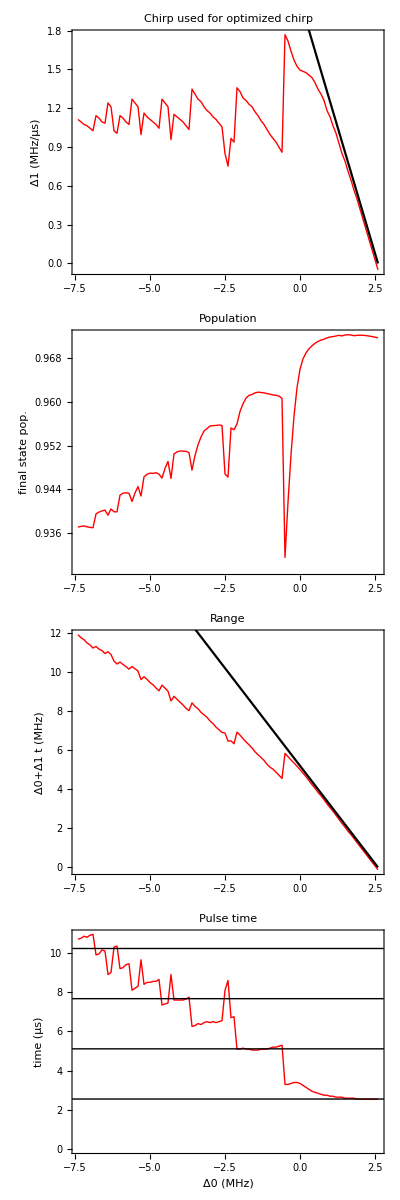

```mathematica
{{Show[ListPlot[Transpose@{optimal⟦All,1⟧,optimal⟦All,2⟧⟦All,2⟧},PlotRange->All,ImageSize->320,FrameLabel->{"","Δ1 (MHz/μs)"},PlotLabel->"Chirp used for optimized chirp",ImagePadding->{{70, 10}, {0, 10}}],Plot[2/τ(shift-Δ0),{Δ0,shift-10,shift},PlotStyle->Black]]},{ListPlot[Transpose@{optimal⟦All,1⟧,optimal⟦All,2⟧⟦All,1⟧⟦All,2⟧},PlotRange->All,ImageSize->320,FrameLabel->{"","final state pop."},PlotLabel->"Population",ImagePadding->{{70, 10}, {0, 10}}]},{Show[ListPlot[Transpose@{optimal⟦All,1⟧,optimal⟦All,2⟧⟦All,1⟧⟦All,1⟧optimal⟦All,2⟧⟦All,2⟧},PlotRange->All,ImageSize->320,FrameLabel->{"","Δ0+Δ1 t (MHz)"},PlotLabel->"Range",ImagePadding->{{70, 10}, {0, 10}}],Plot[2(shift-Δ0),{Δ0,shift-10,shift},PlotStyle->Black,ImageSize->320]]},{ListPlot[Transpose@{optimal⟦All,1⟧,optimal⟦All,2⟧⟦All,1⟧⟦All,1⟧},PlotRange->All,ImageSize->320,FrameLabel->{"Δ0 (MHz)","time (μs)"},PlotLabel->"Pulse time",Epilog->{Line[{{-10,4τ},{5,4τ}}],Line[{{-10,3τ},{5,3τ}}],Line[{{-10,2τ},{5,2τ}}],Line[{{-10,τ},{5,τ}}]}]}}//TableForm
```

```mathematica
optimal⟦78⟧
```

{0.29375,{{3.05,0.969764},1.45508}}

```mathematica
Manipulate[Show[ListPlot[findPops[2π 222 MHz,2π 37 MHz,optimal⟦i⟧⟦1⟧ MHz,optimal⟦i⟧⟦2,2⟧MHz/μs]⟦4⟧⟦All⟧,PlotRange->{0,1},PlotLabel->StringForm["Δ0=``, Δ1=``",optimal⟦i⟧⟦1⟧,optimal⟦i⟧⟦2,2⟧]],ListPlot[findPops[0.95 2π 222 MHz,0.95 2π 37 MHz,optimal⟦i⟧⟦1⟧ MHz,optimal⟦i⟧⟦2,2⟧MHz/μs]⟦4⟧⟦All⟧,PlotRange->{0,1},PlotStyle->Blue,PlotLabel->StringForm["Δ0=``, Δ1=``",optimal⟦i⟧⟦1⟧,optimal⟦i⟧⟦2,2⟧]],ListPlot[findPops[1.05 2π 222 MHz,1.05 2π 37 MHz,optimal⟦i⟧⟦1⟧ MHz,optimal⟦i⟧⟦2,2⟧MHz/μs]⟦4⟧⟦All⟧,PlotRange->{0,1},PlotStyle->Orange,PlotLabel->StringForm["Δ0=``, Δ1=``",optimal⟦i⟧⟦1⟧,optimal⟦i⟧⟦2,2⟧]]],{i,1,Length[optimal],1}]
```

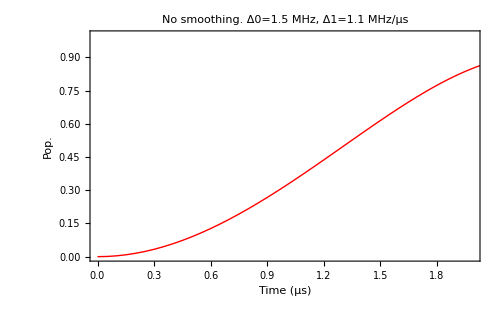

```mathematica
ListPlot[findPops[2π 222 MHz,2π 37 MHz,1.5 MHz,1.1 MHz/μs]⟦4⟧,PlotRange->{{0,2(2.59375-1.5)/1.1},{0,1}},FrameLabel->{"Time (μs)","Pop."},PlotLabel->"No smoothing. Δ0=1.5 MHz, Δ1=1.1 MHz/μs"]
```

```mathematica
Clear[iterp,popAtTime,range]
```

```mathematica
popAtTime[range0_,Δ10_]:=Module[{range=range0,Δ1=Δ10},
iterp=Interpolation[findPops[2π 222 MHz,2π 37 MHz,(shift-range/2) MHz,Δ1 MHz/μs]⟦4⟧];
iterp[range/Δ1]]
```

```mathematica
Δ1test=1.5;ListPlot[Table[{range,popAtTime[range,Δ1test]},{range,0,4,.1}],PlotLabel->StringForm["Chirp centered at Δ_AC for Δ_1=`` MHz/μs",Δ1test],FrameLabel->{"Range (MHz)","Pop"}]
```

NDSolveValue::nlnum: The function value {0.-6.00015 ⅈ,0.-1.16239×10^8 ⅈ,-4.68134-4.02666×10^8 ⅈ,(0.-1. ⅈ) ((0.+0. ⅈ)+(1.49012×10^-8+0. ⅈ) (0.+1.×10^6 shift))} is not a list of numbers with dimensions {4} at {t,p1[t],p2[t],p3[t],p4[t]} = {0.,1.+0. ⅈ,0.+0. ⅈ,1.49012×10^-8+0. ⅈ,1.49012×10^-8+0. ⅈ}.

$Aborted

#### Pulse times

```mathematica
Ωs0=222;
Ωp0=37;
Δ0=1.5;
Δ1=.74;
Ωs[t_,tpulse_,τ_]=Piecewise[{{Ωs0/(√(1+10^6)-√(10^6))(√(1+10^6)-√(((t-tpulse/2)/(tpulse/2))^2+10^6)), 0≤ t<tpulse}, {Ωs0/(√1.3-√(.3))(√1.3-√(((t-1.5tpulse)/(1.5tpulse))^2+0.3)), tpulse+τ≤ t<2tpulse+τ}}];
Ωp[t_,tpulse_,τ_]=Piecewise[{{Ωp0, 0≤ t<tpulse}, {Ωp0, tpulse+τ≤ t<2tpulse+τ}}];
Δ[t_,tpulse_,τ_]=Piecewise[{{Δ0+Δ1 t, 0≤ t<tpulse}, {Δ0+Δ1 tpulse, tpulse≤ t<tpulse+τ}, {Δ0+Δ1 (2tpulse+τ-t), tpulse+τ≤ t<2tpulse+τ}, {Δ0, t≥ 2tpulse+τ}}];
```

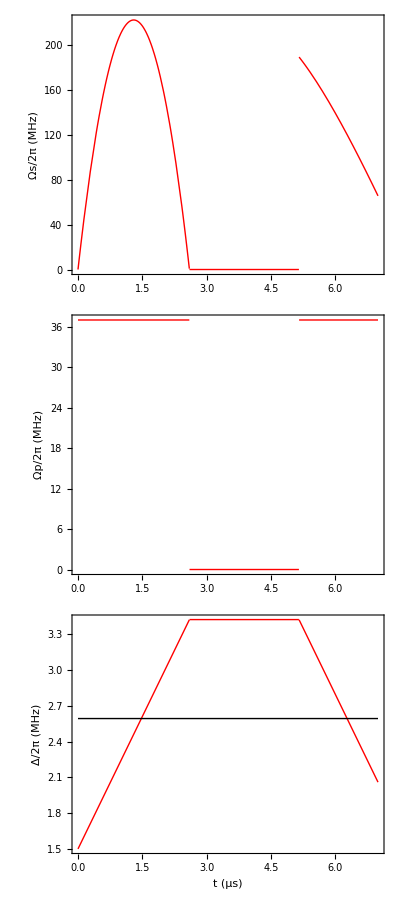

```mathematica
{Plot[Ωs[t,2.6,1],{t,0,7},AspectRatio->.25,ImagePadding->{{50,10},{18,10}},FrameLabel->{"","Ωs/2π (MHz)"}],Plot[Ωp[t,2.6,1],{t,0,7},AspectRatio->.25,ImagePadding->{{50,10},{18,10}},FrameLabel->{"","Ωp/2π (MHz)"}],Plot[Δ[t,2.6,1],{t,0,7},AspectRatio->.25,ImagePadding->{{50,10},{50,10}},FrameLabel->{"t (μs)","Δ/2π (MHz)"},Epilog->Line[{{0,shift},{7,shift}}]]}//TableForm
```

```mathematica
f[y_,tstart_,tpulse_]:=1/0.3235695276781786 Convolve[Exp[-30 t^2],UnitStep[t-tstart]-UnitStep[t-tstart-tpulse],t,y]
```

```mathematica
f[y,0,1]
```

3.09053 (-1/2 √(π/30) (1+Erf[√30 (-1+y)])+1/2 √(π/30) (1+Erf[√30 y]))

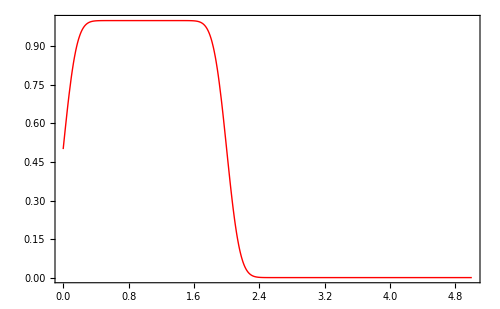

```mathematica
Plot[Evaluate@f[y,0,2],{y,0,5}]
```

```mathematica
-1/2 √(π/30) (1+Erf[√30 (-2+y)])+1/2 √(π/30) (1+Erf[√30 (-1+y)])/.y->1.5
```

0.32357

```mathematica
1.08 10^2-1.12 10^2
```

-4.

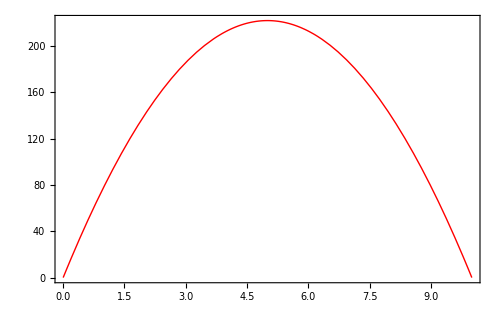

```mathematica
Plot[Ωs0/(√11-√10)(√11-√(((t- 10/2)/(10/2))^2+10)),{t,0,10}]
```

```mathematica
Ωs0/(√11-√10)(√11-√(((t- tpulse/2)/(tpulse/2))^2+10))/.t-> tpulse/2
```

222

```mathematica
sol=Solve[Ωs0/(√11-√10)(√11-√(((t- tpulse/2)/(tpulse/2))^2+10))==222/2,t]
```

{{t→1/4 (2 tpulse-√(-19 tpulse^2+2 √110 tpulse^2))},{t→1/4 (2 tpulse+√(-19 tpulse^2+2 √110 tpulse^2))}}

```mathematica
sol⟦2,1,2⟧-sol⟦1,1,2⟧//FullSimplify//N
```

0.702883 √(tpulse^2)

```mathematica
Solve[0.7028828073375801 tpulse==4,tpulse]
```

{{tpulse→5.69085}}

```mathematica
shift
```

shift

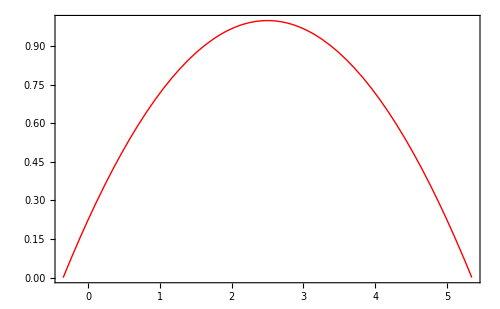

```mathematica
Plot[1/(√11-√10)(√11-√(((Δ-2.5)/(tpulse/2))^2+10))/.tpulse->5.69084911203253,{Δ,-tpulse/2+2.5,1/2 tpulse+2.5}/.tpulse->5.69084911203253]
```

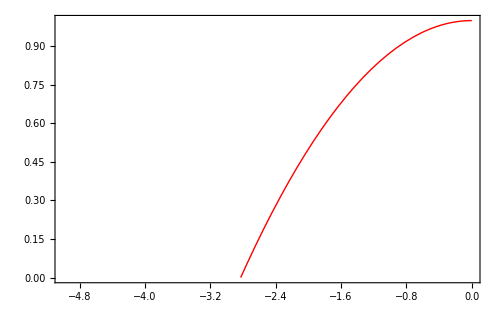

```mathematica
Plot[-.125 x^2+1,{x,-5,0},PlotRange->{0,1}]
```

```mathematica
AOMprofile[Δ
```

```mathematica
(1/1250)^(1/2)//N
```

0.0282843

```mathematica
Solve[2 √(-0.5/a)==4,a]
```

{{a→-0.125}}